```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"Red","Blue","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
Clear[f,dlst,pt,cr,ptlst,M,an,p,x,y]
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
cr3[n_]:=cr3[n]=cols[[n+8]];
cr4[n_]:=cr4[n]=cols[[n+12]];
cr5[n_]:=cr5[n]=cols[[n+16]]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Deking, "Recuurent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 96, section 4.11*)
```

```mathematica
n0=4
```

4

```mathematica
(* substitution *)
```

```mathematica
s[1]={1,2,0,0,0,0,0}; s[2]={3,2,0,0,0,0,0} s[3]={3,4,0,0,0,0,0};s[4]={1,4,0,0,0,0,0};
```

Set::write: Tag Times in {3,2,0,0,0,0,0} s[3] is Protected.

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{1,1,0,0},{0,0,1,1},{0,0,1,0},{1,0,0,1}}

```mathematica
MatrixForm[M]
```

(1 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 1)

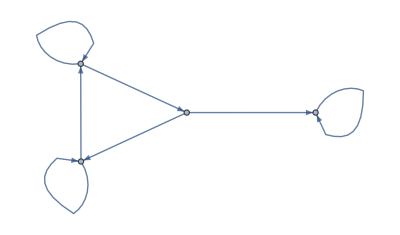

```mathematica
AdjacencyGraph[M]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

1-2 x+3 x^2-3 x^3+x^4

```mathematica
(* solve Polynomial*)
```

```mathematica
NSolve[Det[M-x*IdentityMatrix[n0]]==0,x]
```

{{x→0.122561-0.744862 ⅈ},{x→0.122561+0.744862 ⅈ},{x→1.},{x→1.75488}}

```mathematica
Clear[s]
```

```mathematica
s[1]={1,2}; s[2]={3,2}; s[3]={3,4};s[4]={1,4};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Flatten[Table[s[i],{i,4}]]
```

{1,2,3,2,3,4,1,4}

```mathematica
p[0]={1};p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[19];
```

```mathematica
Length[aa]
```

524288

```mathematica
r=N[Table[{Cos[2*Pi*i/4],Sin[2*Pi*i/4]},{i,4}]]
```

{{0.,1.},{-1.,0.},{0.,-1.},{1.,0.}}

```mathematica
bb=aa /. 1->r[[1] ]/. 2->r[[2]]/. 3->r[[3]]/. 4->r[[4]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g1=ListPlot[cc,ColorFunction->Hue,PlotRange->All,Axes->False,ImageSize->{2000,2000},PlotStyle->PointSize[0.001],AspectRatio->1];
```

```mathematica
Export["Substitution_4symbol_Heighways_Dragon_Complement_tile_level19_g1.jpg",g1]
```

Substitution_4symbol_Heighways_Dragon_Complement_tile_level19_g1.jpg

```mathematica
ptlst=Point[Developer`ToPackedArray[cc],VertexColors->Developer`ToPackedArray[cr/@aa]];
```

```mathematica
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->1,ImageSize->{2000,2000},PlotRange->All];
```

```mathematica
Export["Substitution_4symbol_Heighways_Dragon_Complement_tile_level19_g2.jpg",g2]
```

Substitution_4symbol_Heighways_Dragon_Complement_tile_level19_g2.jpg

```mathematica
dd=ParallelTable[cc[[i]]/(cc[[i]].cc[[i]]),{i,Length[cc]}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
g3=ListPlot[dd,PlotStyle->PointSize[.001],AspectRatio->1,ImageSize->{2000,2000},ColorFunction->"CMYKColors",PlotRange->{{-4,4},{-4,4}}/16];
```

```mathematica
Export["Substitution_4symbol_Heighways_Dragon_Complement_tile_level19_g3.jpg",g3]
```

Substitution_4symbol_Heighways_Dragon_Complement_tile_level19_g3.jpg

```mathematica
ptlst2=Point[Developer`ToPackedArray[dd],VertexColors->Developer`ToPackedArray[cr/@aa]];
```

```mathematica
g4=Graphics[{PointSize[.001],ptlst2},AspectRatio->1,ImageSize->{2000,2000},PlotRange->{{-4,4},{-4,4}}/16];
```

```mathematica
Export["Substitution_4symbol_Heighways_Dragon_Complement_tile_level19_g4.jpg",g4]
```

Substitution_4symbol_Heighways_Dragon_Complement_tile_level19_g3.jpg

```mathematica
Export["Substitution_4symbol_Heighways_Dragon_Complement_tile_level19.jpg",Rasterize[GraphicsGrid[{{g1,g2},{g3,g4}}],"Image",ImageSize->4000]]
```

$Aborted

```mathematica
(*(end)*)
```